# O1: Radioactivity and Counting Statistics

## Priyanka Makin Maya Fabrikant 12/01/2016

## Introduction

In this lab we used a Geiger Counter, which counts the number of gamma particles which hit the Geiger tube, to explore the radioactivity of Thorium. We measured the background radiation counts and then we measured the background plus gamma radiation for a certain amount of time. From this we could calculate the gamma emission rate of the Thorium source. Then, we explored the radioactive penetration through cardboard sheets to find the areal penetration density of the gamma rays.

## Part 1: Measurement of Gamma Rate and Background Rate

```mathematica
RateBack = {65, 67, 82, 76, 81}; (*Background Rate in Counts/Min*)
RBack = (∑_(i=1)^Length[RateBack] RateBack[[i]])/Length[RateBack]//N
δRBack = (√(∑_(i=1)^Length[RateBack] RateBack[[i]]))/Length[RateBack]//N
```

74.2

3.85227

The room has a background rate of (74 ± 4) counts/minute.

```mathematica
RateBackGamma = {113, 135, 112, 125, 109}; (*Background+Gamma Rate in Counts/Min*)
RBackGamma = (∑_(i=1)^Length[RateBackGamma] RateBackGamma[[i]])/Length[RateBackGamma]//N
δRBackGamma = (√(∑_(i=1)^Length[RateBackGamma] RateBackGamma[[i]]))/Length[RateBackGamma]//N
```

118.8

4.87442

The Gamma+Background rate is (119 ± 5) counts/minute.

```mathematica
RGamma = RBackGamma - RBack
δRGamma = √(δRBack^2 + δRBackGamma^2)
```

44.6

6.21289

The thorium source had a gamma emission rate of (45 ± 6) counts/minute.

## Part 2: Penetration of Beta’s Through Cardboard Sheets

```mathematica
RBackBetaGamma = {1812, 1730, 1808, 1822, 1814};
RBackBetaGammaMean = (∑_(i=1)^Length[RBackBetaGamma] RBackBetaGamma[[i]])/Length[RBackBetaGamma]//N;
δRBackBetaGamma = (√(∑_(i=1)^Length[RBackBetaGamma] RBackBetaGamma[[i]]))/Length[RBackBetaGamma]//N;
RBeta = RBackBetaGammaMean - RBackGamma
δRBeta = √(δRBackBetaGamma^2 + δRBackGamma^2)
```

1678.4

19.5755

So, the beta rate is (1680 ± 20) counts/minute.

```mathematica
A = {1, 2, 3, 4, 5, 6}; (*Number of Barriers*)
Rtot = {895, 726, 446, 325, 211, 172}; (*Total Counts/Minute Background+Gamma+Beta*)
δRtot = √Rtot; (*Uncertainty on total counts/minute*)
BetaRate = Rtot - RBackGamma
δBetaRate = √(δRtot^2+ δRBackGamma^2)
```

{776.2,607.2,327.2,206.2,92.2,53.2}

{30.3111,27.3817,21.6739,18.6751,15.3219,13.9914}

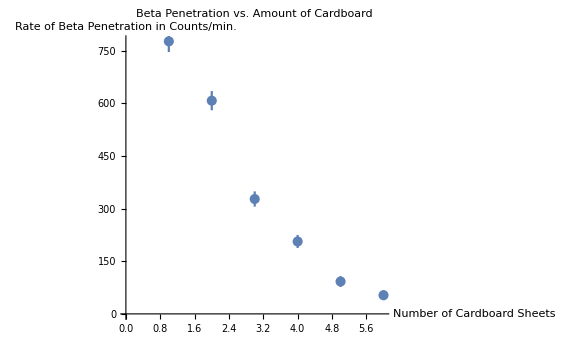

```mathematica
Needs["ErrorBarPlots`"]
xvsy = Thread[{A, BetaRate}];
δy = Table[ErrorBar[δBetaRate[[i]]], {i, 1, Length[A]}];
xvsytotal = Thread[{xvsy, δy}];
ErrorListPlot[xvsytotal, AxesLabel -> {"Number of Cardboard Sheets", "Rate of Beta Penetration in Counts/min."}, PlotLabel -> "Beta Penetration vs. Amount of Cardboard"]
```

```mathematica
(*Data is Entered Here*)
xdata=A;
ydata=BetaRate;
ErrorData=δBetaRate;

(*NO NEED TO ALTER THE REMAINING CODE*)
Needs["ErrorBarPlots`"]

(*Converting the ydata and combining the previous lists*)
L=Length[xdata];
ϵ=Mean[xdata]/10;
xmin=Min[xdata]-ϵ;
xmax=Max[xdata]+ϵ;
ylogdata=Log[ydata]//N;
xylogdata=Thread[{xdata,ylogdata}];
ErrorData2=1/ydata ErrorData;
ErrorData3=Table[ErrorBar[ErrorData2[[i]]],{i,1,L}];
xylogErrordata=Thread[{xylogdata,ErrorData3}];
```

```mathematica
Δ=L*∑_(i=1)^L (xdata[[i]])^2-(∑_(i=1)^L xdata[[i]])^2
```

105

```mathematica
m=1/Δ(L*∑_(i=1)^L (xdata[[i]]*ylogdata[[i]])-(∑_(i=1)^L xdata[[i]])*∑_(i=1)^L ylogdata[[i]])
```

-0.557662

```mathematica
b=1/Δ((∑_(i=1)^L (xdata[[i]])^2*∑_(i=1)^L ylogdata[[i]])-(∑_(i=1)^L xdata[[i]])*(∑_(i=1)^L (xdata[[i]]*ylogdata[[i]])))
```

7.3986

```mathematica
σy=√(1/(L-2)*∑_(i=1)^L (ylogdata[[i]]-(m*xdata[[i]]+b))^2)
```

0.153538

```mathematica
δm=√((L*σy^2)/Δ)
```

0.0367027

```mathematica
δb=√((σy^2*∑_(i=1)^L (xdata[[i]])^2)/Δ)
```

0.142936

In summary:

```mathematica
Grid[{{"m", m}, {"δm", δm}, {"b", b}, {"δb", δb}}, Frame -> All]
```

m | -0.557662
δm | 0.0367027
b | 7.3986
δb | 0.142936

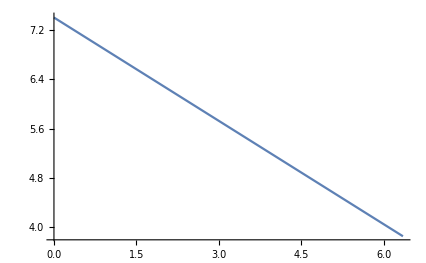

```mathematica
f[X_] := m*X+b
Plot[f[x], {x, 0, xmax}]
```

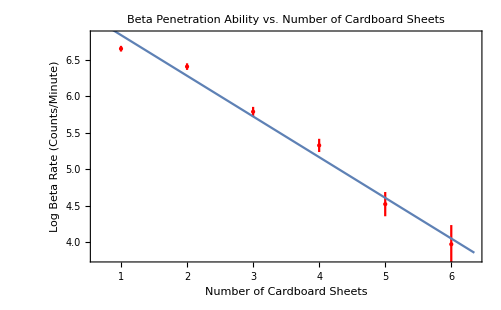

```mathematica
ϵ2=ϵ=Mean[ylogdata]/30;
ymin=Min[ylogdata]-ϵ2;
ymax=Max[ylogdata]+ϵ2;

p1=ErrorListPlot[xylogErrordata,PlotStyle->{Red,PointSize[Small]},PlotRange->{{xmin,xmax},All}];
Show[p1,p2,Frame->True,Axes->False,LabelStyle->{FontFamily->"Times",FontSize->13},FrameLabel->{"Number of Cardboard Sheets","Log Beta Rate (Counts/Minute)"},PlotLabel->"Beta Penetration Ability vs. Number of Cardboard Sheets",FrameStyle->Thickness[0.0027],PlotRange->{ymin,ymax}]
```

The relative error of the count rate increases as the number of sheets increase because the count rate decreases. Also, based on the idea of standard deviation, we know that 68% accuracy is pretty good, meaning 4 out of the 6 bars should have the best fit line going through it. Our data shows 3 of them touching the line which is 50%. Some error could have arisen because of the fact that the cardboard sheets weren’t all uniform. Some of them had a bigger area or a larger thickness/weight as we will see in the following section.

```mathematica
x0 = 1.32; (*Cardboard Thickness in mm*)
δx0 = 0.01; (*mm*)

λ = -x0/m (*Penetration Depth in mm*)
δλ = λ √((δm/m)^2+(δx0/x0)^2) (*Uncertianty on Penetration Depth in mm*)
```

2.36702

0.156815

The penetration depth is (2.4 ± 0.2) mm.

```mathematica
mass = 2.5 ;(*Mass of a Cardboard Sheet in g*)
δmass = 0.1; (*g*)

w = 44.0; (*Width of Cardboard Sheet in mm*)
δw = 0.01;

l = 63.59;(*Length of Cardboard Sheet in mm*)
δl = 0.01;

μ0 = mass/(w*l) (*Areal Density of Cardboard in g/mm^2*)
δμ0 = μ0 √((δmass/mass)^2+(δw/w)^2+(δl/l)^2)(*g/mm^2*)
```

0.000893508

0.0000357412

Thus, the areal density of the cardboard is (9.0 ± 0.4) * 10^-4 g/mm^2.

```mathematica
μp=(μ0*λ)/x0(*Areal Penetration Density in g/mm^2*)
δμp=μp √((δμ0/μ0)^2+(δλ/λ)^2+(δx0/x0)^2)(*g/mm^2*)
```

0.00160224

0.000124589

And the areal penetration density is (1.6 ± 0.1) * 10^-3 g/mm^2.

## Conclusion

In conclusion, I think we were quite successful in calculating the thorium source gamma emission rate in part one of this lab. I am not sure how accurate it is because we have no value to compare it to, but we were successful in measuring it nonetheless. In part 2, we were quite successful in calculating the beta penetration as well because 3 out of 6 uncertainty bars did hit the best fit line. Some error could have arisen because of the fact that the cardboard sheets were quite variable. Some of them had a bigger area than others and the differences between the thickness and, in turn,  weights of the cardboard sheets was quite variable. These factors may have had an effect on our measured areal penetration density.